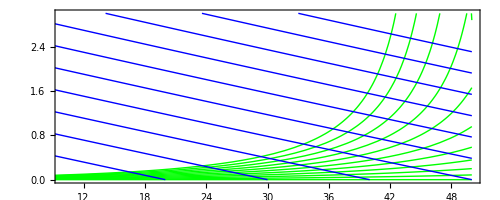

```mathematica
Module[{Psat,P,f1,f2,p1,p2},
Psat[T_]=1000*10^(5.40221-1838.675/(T+241.263));
P=101.325;(*kPa*)

(*f1[T_]=0.622*((ϕ*Psat[T])/(P-ϕ*Psat[T]));*)
f1=Interpolation[Table[{T,Abs[0.622*((ϕ*Psat[T])/(P-ϕ*Psat[T]))]},{T,0,50,0.75}]];
(*f2[T_]=(H-T)/(2500+2*T);*)
f2=Interpolation[Table[{T,100*(H-T)/(2500+2*T)},{T,0,50}]];

p1=Show[Table[{
Plot[f1[DBT],{DBT,0,50},PlotStyle->{Thick,Green},PlotRange->{{10,50},{0,3}}],
(*ListPlot[Table[{DBT,Abs[f1[DBT]]},{DBT,0,50}],Joined->True,PlotStyle->{Thick,Green},PlotRange->{{10,50},{0,3}}],*)
Graphics[]
},{ϕ,0,1,0.1}]];

p2=Show[Table[{
Plot[f2[DBT],{DBT,0,50},PlotStyle->{Thick,Blue},PlotRange->{{10,50},{0,3}}],
(*ListPlot[Table[{DBT,f2[DBT]*100},{DBT,0,50}],Joined->True,PlotStyle->{Thick,Blue},PlotRange->{{10,50},{0,3}}],*)
Graphics[]
},{H,20,110,10}]];(*Show[Table[{
Plot[
Piecewise[{{None,≤f2[DBT]},{f2[DBT],{DBT,0,50},PlotStyle->{Thick,Blue},PlotRange->{{10,50},{0,3}}],
(*ListPlot[Table[{DBT,f2[DBT]*100},{DBT,0,50}],Joined->True,PlotStyle->{Thick,Blue},PlotRange->{{10,50},{0,3}}],*)
Graphics[]
},{H,20,100,10}]];*)

Show[p1,p2,
Frame->True,
AspectRatio->Full,
ImageSize->500]
]
```

```mathematica
Length[Table[t,{t,20,100,20}]]
```

5

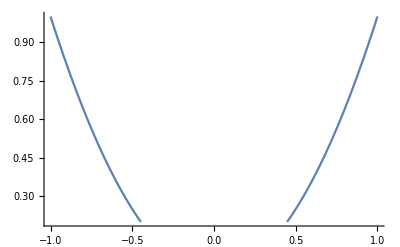

```mathematica
Plot[Piecewise[{{None,x^2<0.2},{x^2,x^2≥0.2}}],{x,-1,1}]
```

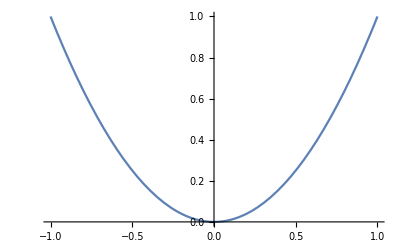

```mathematica
Plot[x^2,{x,-1,1}]
```